```mathematica
σx={{0,1},{1,0}};
σy = {{0,-I},{I,0}}
σp={{0,0},{1,0}};
σm = {{0,1},{0,0}};
id = {{1,0},{0,1}};
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
σm1=KroneckerProduct[σm,id];
σm2=KroneckerProduct[id,σm];
σp1= KroneckerProduct[σp,id];
σp2=KroneckerProduct[id,σp];
```

```mathematica
σpp=σp1+σp2 
σmm=σm1+σm2
```

{{0,0,0,0},{1,0,0,0},{1,0,0,0},{0,1,1,0}}

{{0,1,1,0},{0,0,0,1},{0,0,0,1},{0,0,0,0}}

```mathematica
ψp= 1/Sqrt[2]*{0,1,1,0};
ψm=1/Sqrt[2]*{0,1,-1,0};
```

```mathematica
σmm.{0,0,0,1}
```

{0,1,1,0}

```mathematica
rx1=KroneckerProduct[MatrixExp[I*σx*γ/2],id] ;
rx2=KroneckerProduct[id,MatrixExp[I*σx*δ/2]] ;
ry1=KroneckerProduct[MatrixExp[I*σy*α/2],id] ;
ry2=KroneckerProduct[id,MatrixExp[I*σy*β/2]] ;
```

```mathematica
rx2.ry1.{0,0,1,0} /.{α->π,δ->π}
```

{0,ⅈ,0,0}

```mathematica
rx2 /.{δ->π} // MatrixForm
```

(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)

```mathematica
h2={{-Δ/2,g},{g,Δ/2}}
```

{{-Δ/2,g},{g,Δ/2}}

```mathematica
Eigenvalues[h2]
```

{-1/2 √(4 g^2+Δ^2),1/2 √(4 g^2+Δ^2)}

```mathematica
evs=Assuming[g>0 && Δ>0,FullSimplify[Map[#/Norm[#]&,Eigenvectors[h2]]]]
```

{{-(√(1+Δ/(√(4 g^2+Δ^2))))/(√2),2/(√(8+(2 Δ (Δ+√(4 g^2+Δ^2)))/g^2))},{(-Δ+√(4 g^2+Δ^2))/(g √(8+(2 Δ (Δ-√(4 g^2+Δ^2)))/g^2)),(√(1+Δ/(√(4 g^2+Δ^2))))/(√2)}}

```mathematica
ψp2=1/Sqrt[2]{1,1}
```

{1/(√2),1/(√2)}

```mathematica
ψm2=1/Sqrt[2]{1,-1}
```

{1/(√2),-1/(√2)}

```mathematica
componentsp = {FullSimplify[evs[[1]].ψp2],FullSimplify[evs[[2]].ψp2]};
componentsm = {FullSimplify[evs[[1]].ψm2],FullSimplify[evs[[2]].ψm2]};
```

```mathematica
αswap=Solve[1==FullSimplify[componentsp[[1]]*componentsm[[1]]+α*componentsp[[2]]*componentsm[[2]]],{α}][[1]][[1]][[2]]
```

(Δ-2 √(4 g^2+Δ^2))/Δ

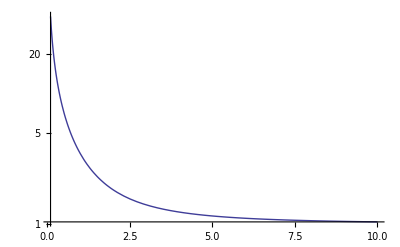

```mathematica
LogPlot[-αswap /.{g->1},{Δ,0.1,10},PlotRange->Full]
```